```mathematica
G=9.81 ;
κ=0.41 ;
λ=0.015;
ASTAR=26.0;
AE=180.0;
BE=1.75;

ϱ=950.0;
ν=3.1*10^(-6);
SLOPE=1.0*10^(-2);
DP=8.0*10^(-3);
ϵb=0.38;

dummyA = - ϱ*BE*ϵb*(1.0-ϵb)/DP;
dummyB = - ϱ*ν*AE*(1.0-ϵb)^2/(ϵb*DP^2);
dummyC = + ϵb*ϱ*G*SLOPE;
Print["#########\nU_bulk = "]
ub = (-dummyB-Sqrt[dummyB^2-4.0*dummyA*dummyC])/(2.0*dummyA)

REG=1.0*10^(-12);

α = -2.0/DP*Log[1.0/0.994-1.0];
ϵ = ϵb+(1.0-ϵb)*0.5*(1.0+Tanh[0.5*α*x]);
ZLS = x+Log[1.0+Exp[-α*x]]/α;

Print["#########\nτv = "]
τv = ϱ*ν*(D[ϵ,z]*u[x]+ϵ*u'[x])

ℓt = κ * ZLS * (1.0-Exp[-Sqrt[ZLS*u[x]/(ν*ASTAR^2)+REG]]);
Print["#########\nτt = "]
τt = ϱ*ϵ*ℓt^2*Sqrt[u'[x]*u'[x]+REG]*u'[x]

Print["#########\nτd = "]
τd = ϱ*λ*DP/(1.0-ϵb)*(1.0-ϵ)*ϵ*u[x]*u'[x]

Print["#########\nf = "]
f = -AE*(1.-ϵ)^2/(ϵ*DP)^2*ϱ*ν*u[x] -BE*(1.-ϵ)/DP*ϱ*Sqrt[u[x]*u[x]+REG]*u[x]

SOURCE = ϵ*ϱ*G*SLOPE + ϵ*f - ϱ*ν*D[ϵ,z]*u'[x];
```

#########
U_bulk =

0.00412714

#########
τv =

0.002945 (0.38+0.31 (1.+Tanh[638.747 x])) u'[x]

#########
τt =

159.695 (1.-ⅇ^(-√(1.×10^-12+477.19 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)]) u[x])))^2 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)])^2 (0.38+0.31 (1.+Tanh[638.747 x])) u'[x] √(1.×10^-12+u'[x]^2)

#########
τd =

0.183871 (0.62-0.31 (1.+Tanh[638.747 x])) (0.38+0.31 (1.+Tanh[638.747 x])) u[x] u'[x]

#########
f =

-(8282.81 (0.62-0.31 (1.+Tanh[638.747 x]))^2 u[x])/(0.38+0.31 (1.+Tanh[638.747 x]))^2-207813. (0.62-0.31 (1.+Tanh[638.747 x])) u[x] √(1.×10^-12+u[x]^2)

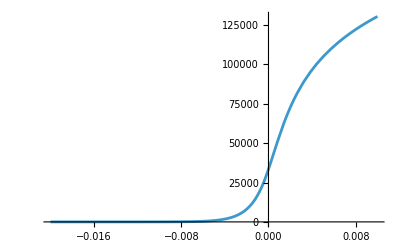

```mathematica
Z0=-0.02;
Z1=0.01;

solution = NDSolve[{0==ϵ*ϱ*G*SLOPE +D[τv+τt+τd,x] + ϵ*f-ϱ*ν*D[ϵ,z]*u'[x],u[Z0]==ub*1.01,u'[Z0]==0.},u[x],{x, Z0, Z1}];
Plot[Evaluate[u[x]/. solution],{x,Z0,Z1},PlotRange->All]
```

```mathematica
AsymptoticDSolveValue[{0==ϵ*ϱ*G*SLOPE +D[τv+τt+τd,x] + ϵ*f-ϱ*ν*D[ϵ,z]*u'[x],u[Z0]==ub*1.01,u'[Z0]==0.},u[x],{x, 0, 1}]
```

AsymptoticDSolveValue::aord: Approximation order specification 0.01 should be a positive integer.

AsymptoticDSolveValue[{0==0.+93.195 (0.38+0.31 (1.+Tanh[638.747 x]))+(0.38+0.31 (1.+Tanh[638.747 x])) (-(8282.81 (0.62-0.31 (1.+Tanh[638.747 x]))^2 u[x])/(0.38+0.31 (1.+Tanh[638.747 x]))^2-207813. (0.62-0.31 (1.+Tanh[638.747 x])) u[x] √(1.×10^-12+u[x]^2))+0.583144 Sech[638.747 x]^2 u'[x]+36.4086 Sech[638.747 x]^2 (0.62-0.31 (1.+Tanh[638.747 x])) u[x] u'[x]-36.4086 Sech[638.747 x]^2 (0.38+0.31 (1.+Tanh[638.747 x])) u[x] u'[x]+0.183871 (0.62-0.31 (1.+Tanh[638.747 x])) (0.38+0.31 (1.+Tanh[638.747 x])) u'[x]^2+31621.5 (1.-ⅇ^(-√(1.×10^-12+477.19 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)]) u[x])))^2 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)])^2 Sech[638.747 x]^2 u'[x] √(1.×10^-12+u'[x]^2)+319.39 (1.-ⅇ^(-√(1.×10^-12+477.19 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)]) u[x])))^2 (1-(1. ⅇ^(-1277.49 x))/(1.+ⅇ^(-1277.49 x))) (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)]) (0.38+0.31 (1.+Tanh[638.747 x])) u'[x] √(1.×10^-12+u'[x]^2)+(159.695 ⅇ^(-√(1.×10^-12+477.19 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)]) u[x])) (1.-ⅇ^(-√(1.×10^-12+477.19 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)]) u[x]))) (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)])^2 (0.38+0.31 (1.+Tanh[638.747 x])) u'[x] (477.19 (1-(1. ⅇ^(-1277.49 x))/(1.+ⅇ^(-1277.49 x))) u[x]+477.19 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)]) u'[x]) √(1.×10^-12+u'[x]^2))/(√(1.×10^-12+477.19 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)]) u[x]))+0.002945 (0.38+0.31 (1.+Tanh[638.747 x])) u''[x]+0.183871 (0.62-0.31 (1.+Tanh[638.747 x])) (0.38+0.31 (1.+Tanh[638.747 x])) u[x] u''[x]+1/(√(1.×10^-12+u'[x]^2))159.695 (1.-ⅇ^(-√(1.×10^-12+477.19 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)]) u[x])))^2 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)])^2 (0.38+0.31 (1.+Tanh[638.747 x])) u'[x]^2 u''[x]+159.695 (1.-ⅇ^(-√(1.×10^-12+477.19 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)]) u[x])))^2 (x+0.000782782 Log[1.+ⅇ^(-1277.49 x)])^2 (0.38+0.31 (1.+Tanh[638.747 x])) √(1.×10^-12+u'[x]^2) u''[x],u[-0.02]==0.00416841,u'[-0.02]==0.},u[x],{x,-0.02,0.01}]